## Read data in

```mathematica
SetDirectory["ADD PATH TO FILES HERE"];
(*single pair*)
files=FileNames["Evo_N1000_M500_mu0.000_nuL_0.010_nuR_*_nur*_rGlob0.50_kon*_koff1.00_f1.00_g0.50_K*n0.0*time*_2_rep*.txt"];
files= files[[Ordering@PadRight@StringSplit[files,x:DigitCharacter..:>FromDigits@x]]];
Length[files]
rEvo1=Table[ReadList[files[[f]],Number],{f,1,Length[files]}]//N;
(**)
files=FileNames["Evo_N1000_M500_mu0.000_nuL_0.010_nuR_*_nur*_rGlob0.50_kon*_koff1.00_f1.00_g0.50_K*n1.0*time*_2_rep*.txt"];
files= files[[Ordering@PadRight@StringSplit[files,x:DigitCharacter..:>FromDigits@x]]];
Length[files]
rEvo2=Table[ReadList[files[[f]],Number],{f,1,Length[files]}]//N;
(**)
files=FileNames["Evo_N1000_M500_mu0.000_nuL_0.010_nuR_*_nur*_rGlob0.50_kon*_koff1.00_f1.00_g0.50_K*n2.0*time*_2_rep*.txt"];
files= files[[Ordering@PadRight@StringSplit[files,x:DigitCharacter..:>FromDigits@x]]];
Length[files]
rEvo3=Table[ReadList[files[[f]],Number],{f,1,Length[files]}]//N;
```

17

17

17

## Take average of M entries from each file

```mathematica
M = 5000;
rStar1=Table[
max=Length[rEvo1[[j]]];
take = Table[i, {i, max-M,max}];
Mean[Flatten[rEvo1[[j,take]]]],{j,1,Length[rEvo1]}];

rStar2=Table[
max=Length[rEvo2[[j]]];
take = Table[i, {i, max-M,max}];
Mean[Flatten[rEvo2[[j,take]]]],{j,1,Length[rEvo2]}];

rStar3=Table[
max=Length[rEvo3[[j]]];
take = Table[i, {i, max-M,max}];
Mean[Flatten[rEvo3[[j,take]]]],{j,1,Length[rEvo3]}];
```

## Average over repeats if applicable

```mathematica
(*repeats = 10;
lists = Table[Table[i, {i,j, j+repeats-1}], {j,1,170-9,repeats}];
rStar1bar=Table[Mean[rStar1[[lists[[i]]]]], {i,1,Length[lists]}];
rStar1sd=Table[StandardDeviation[rStar1[[lists[[i]]]]], {i,1,Length[lists]}];
rStar1se=Table[StandardDeviation[rStar1[[lists[[i]]]]]/Sqrt[Length[rStar1[[lists[[i]]]]]], {i,1,Length[lists]}];

rStar2bar=Table[Mean[rStar2[[lists[[i]]]]], {i,1,Length[lists]}];
rStar2sd=Table[StandardDeviation[rStar2[[lists[[i]]]]], {i,1,Length[lists]}];
rStar2se=Table[StandardDeviation[rStar2[[lists[[i]]]]]/Sqrt[Length[rStar2[[lists[[i]]]]]], {i,1,Length[lists]}];

rStar3bar=Table[Mean[rStar3[[lists[[i]]]]], {i,1,Length[lists]}];
rStar3sd=Table[StandardDeviation[rStar3[[lists[[i]]]]], {i,1,Length[lists]}];
rStar3se=Table[StandardDeviation[rStar3[[lists[[i]]]]]/Sqrt[Length[rStar3[[lists[[i]]]]]], {i,1,Length[lists]}];*)
```

## Evolution over time

```mathematica
(*get average by multiplying by frequency*)
Needs["ErrorBarPlots`"]
kcList = {0.1,0.2, 0.3,0.4, 0.5,0.6, 0.7,0.8,0.9, 1,  1.1,1.2,1.3,1.4,1.5,1.6, 1.7, 1.8, 1.9, 2,2.5,3,4,5,6};
kcList = {0.1,0.5, 0.75, 1,1.5, 2,2.5, 3, 3.5, 4, 4.5, 5,6,7,8,9,10};
kcList = {0.1,0.25, 0.5, 0.75, 1,1.25, 1.5, 2,2.5, 3, 3.5, 4, 4.5, 5,6,7,8};
factor=1;
rStarWITHkc1 = Table[{kcList[[i]], rStar1[[i]]}, {i,1,Length[rStar1]}];
(*rStarWITHkc1er =  Table[{{kcList[[i]], rStar1[[i]]}, ErrorBar[ rStar1[[i]]]}, {i,1,Length[rStar1]}];*)

rStarWITHkc2 = Table[{kcList[[i]], rStar2[[i]]}, {i,1,Length[rStar2]}];
(*rStarWITHkc2er =  Table[{{kcList[[i]], rStar2bar[[i]]}, ErrorBar[ rStar2sd[[i]]]}, {i,1,Length[rStar2bar]}];*)

rStarWITHkc3 = Table[{kcList[[i]], rStar3[[i]]}, {i,1,Length[rStar3]}];
(*rStarWITHkc3er =  Table[{{kcList[[i]], rStar3bar[[i]]}, ErrorBar[ rStar3sd[[i]]]}, {i,1,Length[rStar3bar]}];*)

max=8.5;
```

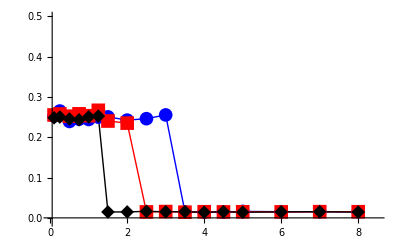

```mathematica
Show[ListPlot[{rStarWITHkc1,rStarWITHkc2,rStarWITHkc3} , Joined->True, PlotRange->{{0.01-0.001,max}, {-0.01,0.5}}, PlotStyle->{{Blue,Thin}, {Red, Thin},{Black, Thin}}, PlotMarkers->{Automatic,14}], AxesStyle->Thickness[0.0025],TicksStyle->Directive[16, Black, FontFamily->"Times"]]
```

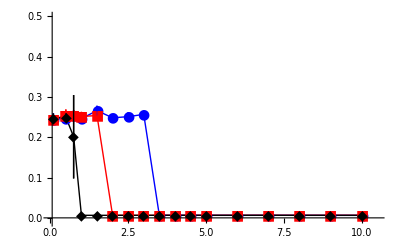

```mathematica
Show[ErrorListPlot[{rStarWITHkc1er,rStarWITHkc2er, rStarWITHkc3er} , Joined->True, PlotRange->{{0.01-0.001,max}, {-0.01,0.5}}, PlotStyle->{{Blue,Thin}, {Red, Thin},{Black, Thin}}, PlotMarkers->{Automatic,14}], AxesStyle->Thickness[0.0025],TicksStyle->Directive[16, Black, FontFamily->"Times"]]
```